# Computer Analysis of Poetry

Mark Greenberg

Christoper Wolfram

## Part 1: Metrical Pattern

Poets pay attention to the natural stresses in words, and sometimes they arrange words so that the stresses form patterns. Typical patterns stress every other syllable (duple meter) or every third syllable (triple meter). A convention exists to further classify poetic lines according to a unit of two or three syllables, called a foot. I choose not to follow this convention, instead looking at the line of poetry as a continuous pattern. The goal of Part 1 is to display the metrical pattern of a stanza of poetry graphically around the printed syllables.

The analyzeMeter function that does this accepts a stanza of English poetry and returns the stress pattern of the syllables. It gets the stress information from the “PhoneticForm” property in WordData and the syllabification information from the “Hyphenation” property. Sometimes words are not in WordData, or the database doesn’t have phonetic or hyphenation values for a word. In those cases we use neural networks to infer the phonetic form and/or syllabification. Also, 1-syllable words are stressed in the database, but minor words like the and and, called “stopwords” in the Wolfram Language, are usually unstressed in context. The code demotes single-syllable stopwords from stressed to undetermined. A combination of replacement rules and the SequencePredict function attempts to resolve syllables that the program has not yet determined to be stressed or unstressed.

## The Phonetic/Syllabification Neural Network

This neural network takes a single word for which WordData can’t provide the phonetic and syllabic information, and returns a phonetic representation in the International Phonetic Alphabet (IPA) along with the original word divided into syllables. It is trained on WordData, which provides 27,811 words that have both phonetic and syllabic information. This set is divided into two subsets, 85% becoming the training set and 15% becoming the test set. The phonetic part of the network is a teacher forcing network, which takes three inputs during training (e.g., “formation”, “>fɔrmˈeɪʃən<”, and {“for”,”ma”,”tion”}). Each character of the English word is fed to a Long Short-Term Memory layer (LSTM). The network tries to predict the next phonetic character, the success of which is fed back to the LSTM. This pattern continues until it encounters the end-of-word character “<”. The gated recurrent layer has a second output for the syllabification of the word, which outputs a list of syllables.

This is what the training data looks like, one input and two outputs.

```mathematica
SeedRandom[1234];
allWords=RandomSample[Select[ToLowerCase[WordData[]],StringMatchQ[LetterCharacter..]]];
allWordsAssocs=Quiet[DeleteMissing[<|"Input"->#,"FullTargetSequence"->WordData[#,"PhoneticForm"],"SyllabicTarget"->WordData[#,"Hyphenation"]|>&/@allWords,1,2]];
netInputData=RandomSample[Fold[#2[#1]&,DeleteMissing[allWordsAssocs,1,2],{
MapAt[">"<>#<>"<"&,{All,"FullTargetSequence"}],
MapAt[ToExpression[Characters[StringJoin[StringReplace[#,{_~~EndOfString->"2",_->"1"}]]]]&,{All,"SyllabicTarget"}]}]];
{train3, test3}= TakeDrop[netInputData, Floor[Length[netInputData]*0.85]] ;
Column[RandomSample[test3,4]]
```

<|Input→militancy,FullTargetSequence→>mˈɪlətənsi<,SyllabicTarget→{1,1,2,2,1,1,2,1,2}|>
<|Input→crowing,FullTargetSequence→>krˈoʊɪŋ<,SyllabicTarget→{1,1,1,2,1,1,2}|>
<|Input→sailfish,FullTargetSequence→>sˈeɪlfˌɪʃ<,SyllabicTarget→{1,1,1,2,1,1,1,2}|>
<|Input→coo,FullTargetSequence→>kˈu<,SyllabicTarget→{1,1,2}|>

Thanks to Timothee Verdier for extensive help with this neural network, which has an unusual architecture and had to be assembled from scratch. Here we distill from WordData all the characters in the International Phonetic Alphabet that are relevant to representing English. This becomes the list of possible characters for the phonetic feedback loop within the neural network.

```mathematica
ipaChars=Sort@DeleteDuplicates@Flatten@Characters[netInputData⟦All,2⟧];
inputEncoder=NetEncoder[{"Characters"}];
targetEncoder=NetEncoder[{"Characters",ipaChars}]
```

NetEncoder[<>]

The net has one configuration for training, which is shown below, and a different configuration for production. In this diagram, we can see the basic structure of the network with two inputs (the training data and the “teacher” data that is fed back to be reprocessed), and two outputs (phonetic and syllabic representations). Clicking on the boxes named phoneticDecoder and sylabicDecoder will reveal the logical structure of the net’s two halves.

```mathematica
net = NetGraph[
	{
	"charEnc" -> NetChain[{
		EmbeddingLayer[32],
		NetBidirectionalOperator[LongShortTermMemoryLayer[64]]
		}],
	"phoneticDec" -> NetGraph[
		{
		SequenceLastLayer[],
		EmbeddingLayer[32],
		GatedRecurrentLayer[128],
		NetMapOperator[LinearLayer[]],
		SoftmaxLayer[]
		}
		,
		{ 
			NetPort["State"]-> 1 -> NetPort[3,"State"],
			NetPort["Input"]-> 2 -> 3 -> 4 -> 5 -> NetPort["phoneticOutput"]
			}
		],
	"sylabicDec" -> NetGraph[
		{
		SequenceLastLayer[],
		GatedRecurrentLayer[128],
		NetMapOperator[LinearLayer[2]],
		SoftmaxLayer[]
		}
		,
			{ 
			NetPort["Input"] -> 1 -> NetPort[2, "State"],
			NetPort["Input"] -> 2 -> 3 -> 4 -> NetPort["sylabicOutput"]
			}
		]
	}
	,
	{
	"charEnc" -> NetPort["phoneticDec", "State"],
	"charEnc" -> "sylabicDec",
	NetPort["Target"]-> NetPort["phoneticDec", "Input"]
	}
	,
	"Input" -> inputEncoder
	]
```

NetGraph[<>]

What the last diagram showed is then boxed and called studentNet so it can be embedded within the apparatus needed during training of the network. Notice that instead of two output ports, this “loss” version has a single output so it can keep track of the combined loss value of the syllabic and phonetic sides.

```mathematica
lossNet = NetGraph[
	<|
	"studentNet"-> net
	, "sylabicLoss" -> CrossEntropyLossLayer["Index"]
	, "phoneticLoss" -> CrossEntropyLossLayer["Index"]
	, "toPredict" -> SequenceRestLayer[]
	, "previousAnswer" -> SequenceMostLayer[]
	, "finalLoss" -> ThreadingLayer[Plus]
	|>
	,
	{
	NetPort["FullTargetSequence"] -> "toPredict" -> NetPort["phoneticLoss", "Target"],
	NetPort["FullTargetSequence"] -> "previousAnswer" -> NetPort["studentNet", "Target"],
	NetPort["studentNet", "phoneticOutput"] -> NetPort["phoneticLoss", "Input"],
	NetPort["studentNet", "sylabicOutput"] -> NetPort["sylabicLoss", "Input"],
	NetPort["SylabicTarget"] -> NetPort["sylabicLoss", "Target"],
	{"phoneticLoss", "sylabicLoss"} -> "finalLoss" -> NetPort["Loss"]
	},
	"FullTargetSequence" -> targetEncoder
]
```

NetGraph[<>]

The network is trained on 85% of the data collected from WordData, the remaining 15% held back for testing purposes. We halt the training after eighteen rounds because the validation loss stops improving. Continuing the training beyond that point causes overfitting, a sort of memorization of the training data rather than a holistic fitting of the features.

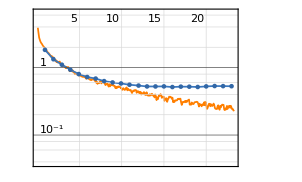
NetTrain Results
summary | ,,  batches:17213  rounds:24  time:4.6min  examples/s:2013
data | ,,  training examples:23639  validation examples:4172  processed examples:550816  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:2.55×10^-1
validation | ,,  loss:5.29×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netTrainRes=NetTrain[lossNet,<|"Input"->train3⟦All,1⟧,"FullTargetSequence"->train3⟦All,2⟧, "SylabicTarget" ->train3⟦All,3⟧|>,All, ValidationSet-><|"Input"->test3⟦All,1⟧,"FullTargetSequence"->test3⟦All,2⟧,"SylabicTarget" ->test3⟦All,3⟧|>, MaxTrainingRounds->50]
```

Now for the process Timothee calls surgery, cutting the part of the network that does the actual generation from the training apparatus. Note that the names of the functions mostly contain “Delete”, ”Replace”, and “Extract.”

```mathematica
trainedNet2=netTrainRes["TrainedNet"];
phoTeachNet=NetDelete[trainedNet2, {"sylabicLoss", "finalLoss"}];
generationNet = NetDelete[trainedNet2, {"phoneticLoss","sylabicLoss", "finalLoss", "toPredict"}];
wordEncoding=NetChain[{NetExtract[generationNet, {"studentNet", 1}]}, "Input"-> NetExtract[generationNet, "Input"]];
phoneticDec = NetReplacePart[NetDelete[NetExtract[generationNet, {"studentNet", "phoneticDec"}],1],"Input"-> NetExtract[phoTeachNet,"FullTargetSequence"]];
phoneticDec = NetReplacePart[NetRename[NetAppend[NetFlatten[phoneticDec], SequenceLastLayer[]], {NetPort["Input"]-> NetPort["PrevPhoneticChar"]}], "Output" -> NetDecoder[{"Class", targetEncoder[["Encoding"]]}]];phoneticDec = NetReplacePart[NetDelete[NetExtract[generationNet, {"studentNet", "phoneticDec"}],1],"Input"-> NetExtract[phoTeachNet,"FullTargetSequence"]];
phoneticDec = NetReplacePart[NetRename[NetAppend[NetFlatten[phoneticDec], SequenceLastLayer[]], {NetPort["Input"]-> NetPort["PrevPhoneticChar"]}], "Output" -> NetDecoder[{"Class", targetEncoder[["Encoding"]]}]];phoneticDec = NetReplacePart[NetDelete[NetExtract[generationNet, {"studentNet", "phoneticDec"}],1],"Input"-> NetExtract[phoTeachNet,"FullTargetSequence"]];
phoneticDec = NetReplacePart[NetRename[NetAppend[NetFlatten[phoneticDec], SequenceLastLayer[]], {NetPort["Input"]-> NetPort["PrevPhoneticChar"]}], "Output" -> NetDecoder[{"Class", targetEncoder[["Encoding"]]}]];
syllabicDec = NetExtract[generationNet, {"studentNet", "sylabicDec"}];
toStrChunks[x_Integer,y_] := {x,y};
toStrChunks[x_List,y_] := {Last[x]+1, y};
```

And finally the function to call the neural network along with some sample results. Execute the code again (shift + return or shift + enter) to see a different set of words.

```mathematica
getPhonsAndSylls[word_String]:= Block[
{previousAnswer = ">", phonetic = "", syllabic},
Module[{wordenc = wordEncoding[word],stateNet},
(* decode the syllables *)
syllabic = Flatten@Position[syllabicDec[wordenc], {pNonBreack_, pBreack_} /; pBreack>pNonBreack];
syllabic = StringTake[word, Rest@FoldList[toStrChunks, 1, syllabic]];
(* decode the phonetic *)
stateNet = NetStateObject[phoneticDec, <|{2, "State"}:> Last@wordenc|>];
While[previousAnswer =!= "<",
previousAnswer = stateNet[previousAnswer];
phonetic = phonetic<>previousAnswer];
<|"Phonetic" -> StringDrop[phonetic, -1], "Syllables" -> syllabic|>]];
testSample=RandomSample[test3,10]⟦All,1⟧;
outputSample=Flatten[{#,Values[getPhonsAndSylls[#]]},1]&/@testSample;
sampleDataset=Dataset[{<|"input"->#⟦1⟧,"phonetic"->#⟦2⟧,"syllabic"->#⟦3⟧|>}&/@outputSample]
```

Dataset[<>]

The error rate of this neural network is about 9.9% on the phonetic output and 4.1% on the syllabic. The phonetic error is somewhat high, but as this is a backup for words without the “PhoneticForm” property in WordData, the errors will impact the performance of the analysis only rarely. Improvements may be achieved by training the neural net with a larger set of data or tweaking its parameters.

## Analysis of Meter

The first stanza of Edgar Allan Poe' s "The Raven" will serve as our example for analyses. This was copied from a website, www.poetryfoundation.org/poems/48860/the-raven. I changed only the appearance of new-lines from literal breaks to “\n”. Punctuation, capitalization, and quotation marks will all be processed by the analyzing code.

```mathematica
stanza="Once upon a midnight dreary, while I pondered, weak and weary,\nOver many a quaint and curious volume of forgotten lore—\nWhile I nodded, nearly napping, suddenly there came a tapping,\nAs of some one gently rapping, rapping at my chamber door.\n“’Tis some visitor,” I muttered, “tapping at my chamber door—\nOnly this and nothing more.”";
```

We extract the meter, phonetic representation, and syllabification for each word of the poem. The first ten are shown here. Some subtleties include identification of one-syllable stop words, which are marked as stressed in WordData but often not stressed in context, and a cross-check between the meter and syllables to make sure they agree.

```mathematica
ipaVowels={"aɪ","aʊ","eɪ","ɔɪ","oʊ","ɐ","ɑ","ɒ","ɔ","ɘ","ə","ɛ","ɜ","ɝ","ɞ","ɤ","ɨ","ɪ","ɯ","ɵ","ɶ","ʉ","ʊ","ʌ","ʏ","a","æ","e","i","o","œ","ø","u","y"};oneSylStops=Select[DeleteMissing[WordData[#,"PhoneticForm"]&/@WordData[All,"Stopwords"]],StringCount[#,ipaVowels]<2&];
getPhoneticForm[word_]:=Module[{phoneticForm},WordData[ToLowerCase[word],"PhoneticForm"]/._Missing->getPhonsAndSylls[word]["Phonetic"]];
getMeter[phon_]:=Module[{ipaSylCt},
If[MemberQ[oneSylStops,phon],Return[{.5}]];
ipaSylCt=StringCount[phon,ipaVowels];
If[ipaSylCt==1,{1},
vowelSounds=StringCases[phon,"ˈ"|"ˌ"...~~ipaVowels];
#/.{a_/;StringContainsQ[a,"ˈ"]->1,a_/;StringContainsQ[a,"ˌ"]->.5,_->0}&/@vowelSounds]];
getSyllables[word_]:=Module[{syllables,phonCheck,part1,part2},
phonCheck=StringCount[getPhoneticForm[word],ipaVowels];
If[phonCheck≤1,Return[{word}]];
syllables=WordData[ToLowerCase[word],"Hyphenation"]/._Missing->getPhonsAndSylls[ToLowerCase[word]]["Syllables"];
If[Length[syllables]==1&&phonCheck==2,vowels={"a","e","i","o","u"};
part1=StringCases["over",StartOfString~~Except[vowels]...~~vowels..]⟦1⟧;
part2=StringDelete["over",StartOfString~~Except[vowels]...~~vowels..];
Return[{part1,part2}],Return[syllables]]];
getWordInfo[word_]:=Module[
{phon=getPhoneticForm[ToLowerCase[word]]},
{word,getMeter[phon],getSyllables[word],phon}];
first10words=Take[TextWords[ToLowerCase[stanza]],10];
first10info=getWordInfo[#]&/@first10words;
first10assoc=<|"word"->#⟦1⟧,"meter"->#⟦2⟧,"syllables"->#⟦3⟧,"phonetics"->#⟦4⟧|>&/@first10info//Dataset
```

Dataset[<>]

We have labeled each syllable that is definitely stressed with a 1, and each that is definitely unstressed with a zero. Ambiguous syllables we have marked with .5. Stress patterns are binary, so we must resolve the .5 syllables to either 1 or 0. We use a two-tier approach for this. First we apply a series of six replacement rules because English prefers not to run three stressed or three unstressed syllables consecutively. After that, I apply the SequencePredict function to find which of the possible remaining patterns best matches known poetic forms (the duple meter and triple meter mentioned at the beginning). No ambiguous syllable stresses remain after that step.

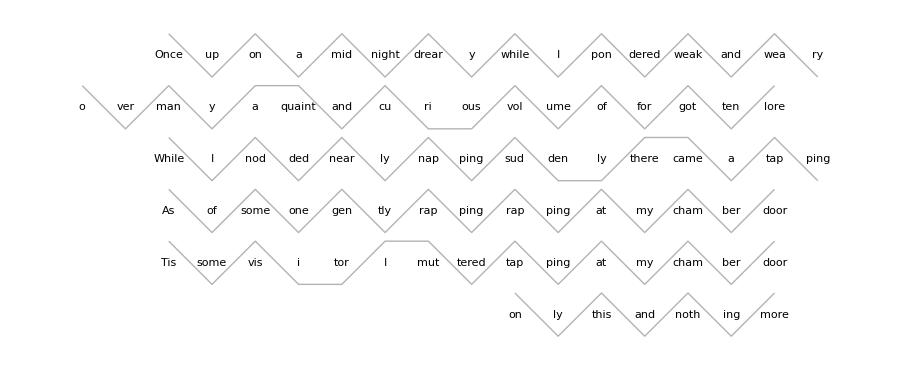

```mathematica
iambic=Table[Flatten[Table[{0,1},n]],{n,1,12}];
trochaic=RotateLeft[#]&/@iambic;
anapestic=Table[Flatten[Table[{0,0,1},n]],{n,1,12}];
dactylic=RotateRight[#]&/@anapestic;
allPatterns=Join[iambic,trochaic,anapestic,dactylic];
analyzeMeter[stanza_]:=(
lines=StringSplit[stanza,EndOfLine];
words=TextWords[#]&/@lines;
wordInfo=Map[getWordInfo[#]&,words,{2}];
meter1=Flatten[#]&/@wordInfo⟦All,All,2⟧;
meter2=meter1//.{
{a___,1,1,1,b___}->{a,1,0,1,b},
{a___,1,1,.5,b___}->{a,1,1,0,b},
{a___,.5,1,1,b___}->{a,0,1,1,b},
{a___,0,0,0,b___}->{a,0,1,0,b},
{a___,0,0,.5,b___}->{a,0,0,1,b},
{a___,.5,0,0,b___}->{a,1,0,0,b}} ;
midCts=Count[#,.5,2]&/@meter2;
zero1s=Tuples[{0,1},#]&/@midCts;
midPos=Flatten[Position[#,.5]]&/@meter2;
prelim=MapIndexed[{midPos⟦#2⟦1⟧⟧,#1}&,zero1s,{2}];
repRules=Map[(Rule@@@Partition[Riffle@@#,2]&),prelim,{2}];
replaced=MapIndexed[ReplacePart[meter2⟦#2⟦1⟧⟧,#1]&,repRules,{2}];
seqPredict=SequencePredict[allPatterns];
result=seqPredict[#,"SequenceProbability"]&/@replaced;
resultPos=Position[#,Max[#]]⟦1,1⟧&/@result;
meter3=MapIndexed[replaced⟦#2,#1⟧⟦1⟧&,resultPos];
alignPt=Max[Position[#,1]]&/@meter3;
splitMeters=Partition[#,UpTo[Max[Position[#,1]]]]&/@meter3;
bkOff=Min[Position[Reverse[#],1]]&/@meter3;
coords=Flatten[MapIndexed[If[
#2⟦2⟧==1,
{1-#2⟦3⟧,#1+1.2 (#2⟦1⟧-1)},
{#2⟦3⟧-1,#1+1.2 (#2⟦1⟧-1)}
]&,Reverse[MapAt[Prepend[1],MapAt[Reverse,splitMeters/.({lhs_List}:>{lhs,{}}),{All,1}],{All,2}]],{3}],1];
xRuns=Range[Length[#]]&/@meter3;
lens=Length/@meter3;
endPts=bkOff;
begPts=endPts-lens;
coordsX=MapThread[Range[#1,#2]&,{begPts+1,endPts}];
coordsY=MapIndexed[{#1+1.2*#2⟦1⟧}⟦1⟧&,Reverse[meter3]];
coords2=MapThread[Partition[Riffle[#1,#2],2]&,{Reverse[coordsX],coordsY}];
txtCoo=MapIndexed[{#1⟦1⟧,1.2*#2⟦1⟧+.5}&,coords2,{2}];
syllab=#⟦;;,3⟧&/@Reverse[wordInfo];
textGr=MapThread[Style[Text[#1,#2],15,FontFamily->"Times"]&,{Flatten[syllab],Partition[Flatten[txtCoo,2],2]}];
meterGraphic=Graphics[{GrayLevel[.7],Line[coords2],Black,textGr},ImageMargins->{{10,10},{0,0}},ImageSize->900]
);
analyzeMeter[stanza]
```

The zigzag lines zig up for stressed syllables and down for unstressed. The last stressed syllable of each line is aligned because this will make the end rhyme more apparent in Part 2 of the project. The program’s analysis of this stanza matches exactly traditional scansion except for one mistake in syllabification, which it marks with the number 11, and the word “a” in the second line which should be unstressed. Poe is using a duple meter pattern, which alternates stressed and unstressed syllables. The graphic shows clearly that the overall framework alternates stressed-unstressed-stressed.... Where there are deviations from this pattern, the poet deliberately added an extra syllable or introduced an unexpected stress. I suggest that this graphic makes more metrical information readily available than the traditional method of marking feet above a line of text.

## Part 2: Rhyme

Poems often rhyme. A naive explanation of rhyme says that one word rhymes with another if the ending sounds are the same, particularly the last vowel sounds and beyond. Rhyme in context is more complicated than that, and the concept of rhyme can be extended to a larger class of what we might call sound echoes. Inside a poem, we really are not rhyming one word with another. Instead, we rhyme one part of the stress pattern with another. It is always the same part of the pattern, a stressed syllable followed by zero to two unstressed syllables. With this definition, we can understand rhymes like “...pick it...” with “thicket” and “Lenore” with “nevermore”. The term rhyme can include a larger family of sound features in a poem. Here, we will consider traditional rhyme (end rhyme), alliteration (front rhyme), assonance (vowel rhyme), and consonance (consonant rhyme). Poets are certainly aware of these echoic features, often plying them for effect. With the help of the Wolfram Language, we will attempt to represent these rhymes in an informative way.

The neural network in Part 1 gives the phonetic representation of the entire word and the word separated into syllables. To map the sound features of the poem, we need also the phonetic representation of each syllable. Several solutions to this problem are possible. We could modify the neural network to give a third output of phonetic syllables. We could use each word’s phonetic representation and split it into the right number of syllables. This would maintain the proper phoneme sounds, but it would often divide the consonants differently than the plain English syllables. A better solution is to get a phonetic representation of the individual syllables we have already. This solution is not perfect, but it does give divisions that are consistent with the scheme we are using.

We create an indexed list of all the phonetic syllables and then use the Subsets function to get a list of all 3655 possible pairs.

```mathematica
syllab2=Flatten[#]&/@Reverse[syllab];
phonSylls=Flatten[MapIndexed[{StringDelete[WordData[#1,"PhoneticForm"]/._Missing->getPhonsAndSylls[#1]["Phonetic"],"ˈ"|"ˌ"],#2}&,syllab2,{2}],1];
allPairs=Subsets[phonSylls,{2}];
{Short[phonSylls],Short[allPairs]}//Column
```

{{nɛ,{1,1}},{ʌp,{1,2}},{ɒn,{1,3}},{ə,{1,4}},{mɪd,{1,5}},«76»,{ðɪs,{6,3}},{ænd,{6,4}},{nɒθ,{6,5}},{ɪŋ,{6,6}},{mɔr,{6,7}}}
{{{nɛ,{1,1}},{ʌp,{1,2}}},{{nɛ,{1,1}},{ɒn,{1,3}}},«3651»,{{nɒθ,{6,5}},{mɔr,{6,7}}},{{ɪŋ,{6,6}},{mɔr,{6,7}}}}

We can find the various kinds of echoes. For now we will not consider the stress values of the syllables. There are 185 alliterative pairs, but only 19 close enough to be heard as echoic features of the poem.

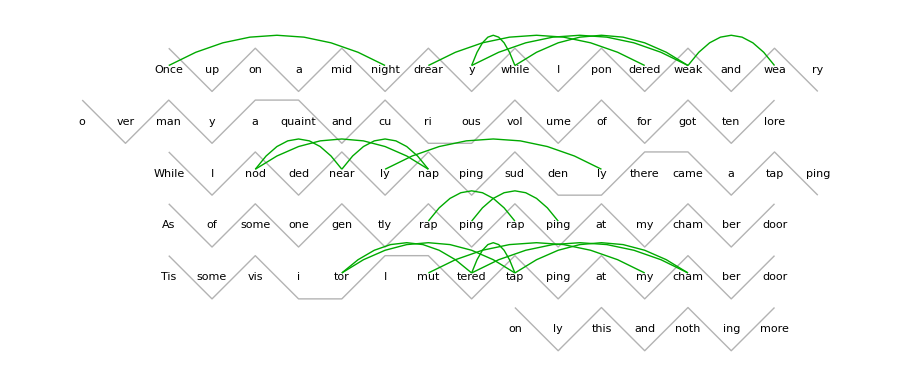

```mathematica
alliterationAll=Cases[allPairs,{{ps1_,_},{ps2_,_}}/;Characters[StringDelete[ps1,"ˈ"|"ˌ"]]⟦1⟧==Characters[StringDelete[ps2,"ˈ"|"ˌ"]]⟦1⟧];
alliterationClose=Cases[alliterationAll,{{_,{l1_,s1_}},{_,{l2_,s2_}}}/;l1===l2&&Abs[s2-s1]<6];
alliterationCoords={Reverse[txtCoo]⟦#⟦1,2,1⟧,#⟦1,2,2⟧⟧,Reverse[txtCoo]⟦#⟦2,2,1⟧,#⟦2,2,2⟧⟧}&/@alliterationClose;
alliterationArcs=BezierCurve[{#⟦1⟧+{0,.1},Mean[{#⟦1⟧,#⟦2⟧}]+{0,1.5},#⟦2⟧+{0,.1}}]&/@alliterationCoords;
Show[meterGraphic,Graphics[{Darker[Green],alliterationArcs}]]
```

Some alliterations ring louder than others, and we can analyze that too. If the alliteration is between two stressed syllables, then we hear the echo clearly. If not, then the echo is faint. This could be represented by line thickness or transparency.

For consonance, which is the repetition of consonant sounds anywhere in two syllables, we change the code slightly.

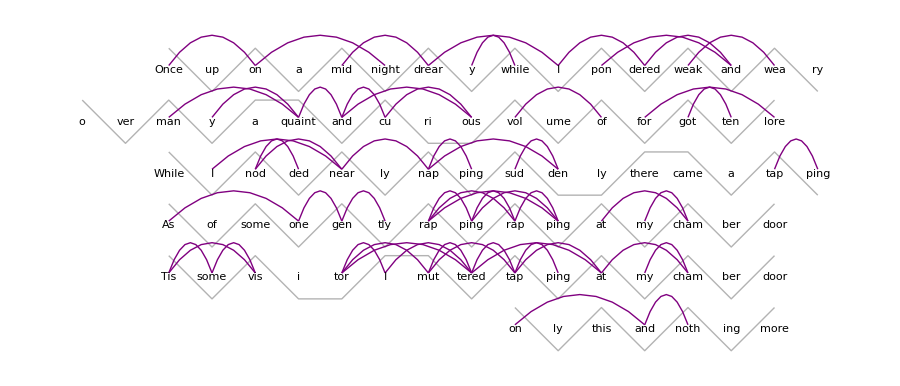

```mathematica
allPhonemes=ipaChars/.("<"|">"|"ˈ"|"ˌ")->Nothing;
ipaConsonants=Complement[allPhonemes,ipaVowels];
consonanceAll=Cases[allPairs,{{ps1_,_},{ps2_,_}}/;Length[Intersection[Characters[ps1],Characters[ps2],ipaConsonants]]>0];
consonanceClose=Cases[consonanceAll,{{_,{l1_,s1_}},{_,{l2_,s2_}}}/;l1===l2&&Abs[s2-s1]<4];
consonanceCoords={Reverse[txtCoo]⟦#⟦1,2,1⟧,#⟦1,2,2⟧⟧,Reverse[txtCoo]⟦#⟦2,2,1⟧,#⟦2,2,2⟧⟧}&/@consonanceClose;
consonanceArcs=BezierCurve[{#⟦1⟧+{0,.1},Mean[{#⟦1⟧,#⟦2⟧}]+{0,1.5},#⟦2⟧+{0,.1}}]&/@consonanceCoords;
Show[meterGraphic,Graphics[{Purple,consonanceArcs}]]
```

And again for assonance, the echo of vowel sounds, the code is slightly different.

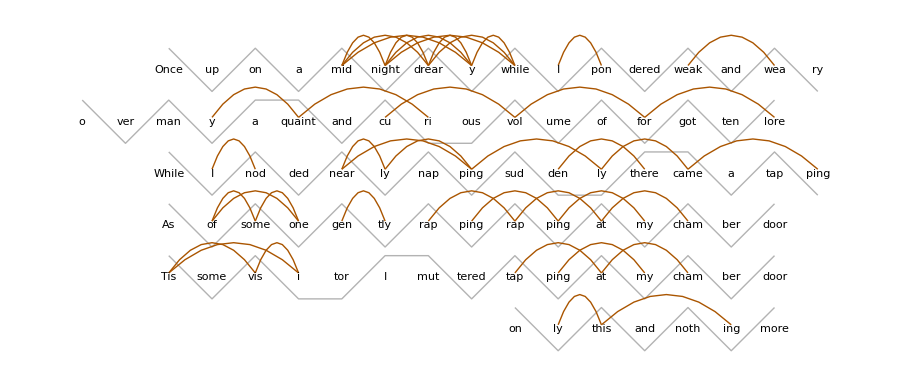

```mathematica
assonanceAll=Cases[allPairs,{{ps1_,_},{ps2_,_}}/;Length[Intersection[Characters[ps1],Characters[ps2],ipaVowels]]>0];
assonanceClose=Cases[assonanceAll,{{_,{l1_,s1_}},{_,{l2_,s2_}}}/;l1===l2&&Abs[s2-s1]<4];
assonanceCoords={Reverse[txtCoo]⟦#⟦1,2,1⟧,#⟦1,2,2⟧⟧,Reverse[txtCoo]⟦#⟦2,2,1⟧,#⟦2,2,2⟧⟧}&/@assonanceClose;
assonanceArcs=BezierCurve[{#⟦1⟧+{0,.1},Mean[{#⟦1⟧,#⟦2⟧}]+{0,1.5},#⟦2⟧+{0,.1}}]&/@assonanceCoords;
Show[meterGraphic,Graphics[{Darker[Orange],assonanceArcs}]]
```

The echoes of traditional end rhyme, what we commonly think of as rhyme, are more difficult to map because they can span multiple lines, they involve groups of syllables, and they are restricted to certain parts of the metrical pattern. This takes some prep work. We will gather a list of rhyme candidates and then test them for identical phonetic endings.

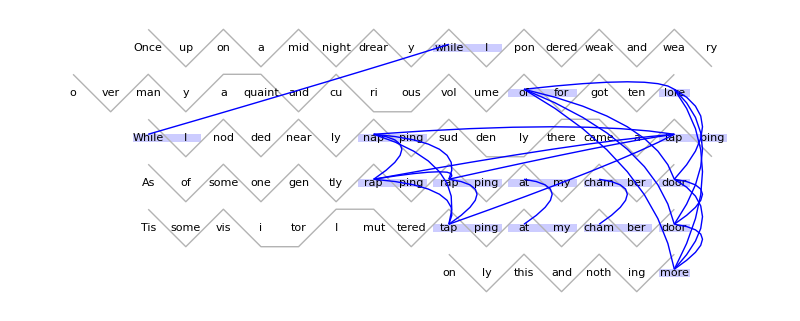

```mathematica
phonSyllsMeter=MapThread[Append[#1,#2]&,{phonSylls,Flatten[meter3]}];
endRhymeMultiCans=SequenceCases[phonSyllsMeter,{{_,_,1},{_,_,0},Repeated[{_,_,0},{0,1}]}];
endRhymeMultiSwords={#⟦1,1⟧<>#⟦2,1⟧,{#⟦1,2⟧,#⟦-1,2⟧}}&/@endRhymeMultiCans;
endRhymeUniCans=Append[#⟦1⟧&/@SequenceCases[phonSyllsMeter,{{_,{a_,_},1},{_,{b_,_},_}}/;a≠b],phonSyllsMeter⟦-1⟧];
endRhymeUniSwords={#⟦1⟧,{#⟦2⟧,#⟦2⟧}}&/@endRhymeUniCans;
endRhymeSwords=Join[endRhymeMultiSwords,endRhymeUniSwords];
endRhymeSubsets=Subsets[endRhymeSwords,{2}];
endRhymes=Cases[endRhymeSubsets,{{s1_,_},{s2_,_}}/;StringContainsQ[s1,StringDelete[s2,StartOfString~~ipaConsonants...]]];
endRhymeBgLt=Rectangle[Reverse[txtCoo]⟦#⟦1,2,1,1⟧,#⟦1,2,1,2⟧⟧+{-.4,-.1},Reverse[txtCoo]⟦#⟦1,2,2,1⟧,#⟦1,2,2,2⟧⟧+{.4,.1}]&/@endRhymes;
endRhymeBgRt=Rectangle[Reverse[txtCoo]⟦#⟦2,2,1,1⟧,#⟦2,2,1,2⟧⟧+{-.4,-.1},Reverse[txtCoo]⟦#⟦2,2,2,1⟧,#⟦2,2,2,2⟧⟧+{.4,.1}]&/@endRhymes;
endRhymeBg=Join[endRhymeBgLt,endRhymeBgRt];
endRhymeCoords={Reverse[txtCoo]⟦#⟦1,2,1,1⟧,#⟦1,2,1,2⟧⟧,Reverse[txtCoo]⟦#⟦2,2,1,1⟧,#⟦2,2,1,2⟧⟧}&/@endRhymes;
endRhymeArcs=BezierCurve[{#⟦1⟧+{0,.1},Mean[{#⟦1⟧,#⟦2⟧}]+{1.5,.5},#⟦2⟧+{0,.1}}]&/@endRhymeCoords;
Show[Graphics[{RGBColor[.8,.8,1],endRhymeBg}],meterGraphic,Graphics[{Blue,endRhymeArcs}],ImageSize->800]
```

One might object that rapping doesn’t rhyme with rapping. It does echo, so I included such repetitions. Eliminating them is as simple as adjusting the matching criterion in the line that begins endRhymes = .

## Conclusion

With a computer we can inspect more than just a poem’s meter and rhyme. The placement of natural stops and the poet’s tendency to twist expected syntax also await computational analysis, but those are paths to be explore another time.

It is easy to get drawn into thinking that poems are these beautiful flowers of emotional expression and miss the craft that molds them from natural language. If we had a way to see some of that craft, to extract and visualize the interplay between sculptor and verbal clay, perhaps that would lead to a better understanding... and maybe even a deeper appreciation. Isn’t a flower that much more wonderful if you recognize the Fibonacci sequence swirling around its center?